# Strings

## Basic Exercises

### Question Subsection

Given the following random words, sort them by the length of the word in ascending order.

```mathematica
randomWords=RandomWord[50]
```

{awn,gorgeously,egret,covering,engender,lariat,behead,fixation,monotheistic,adjust,entrails,renting,pushpin,stable,convince,overwrought,undertaking,pantry,hardcover,fancy,slurred,curricular,premeditate,repairer,repeated,bloodstained,dried,tardily,peignoir,changeless,radially,spiritualistic,picking,lectern,scamper,teasing,meniscus,demureness,stargazer,brokenhearted,glib,statutorily,sandwich,champagne,unsteady,grab,barbershop,cause,cutely,dairying}

#### Hint

Take a look at SortBy.

#### Solution

```mathematica
SortBy[randomWords,StringLength]
```

{awn,glib,grab,cause,dried,egret,fancy,adjust,behead,cutely,lariat,pantry,stable,lectern,picking,pushpin,renting,scamper,slurred,tardily,teasing,convince,covering,dairying,engender,entrails,fixation,meniscus,peignoir,radially,repairer,repeated,sandwich,unsteady,champagne,hardcover,stargazer,barbershop,changeless,curricular,demureness,gorgeously,overwrought,premeditate,statutorily,undertaking,bloodstained,monotheistic,brokenhearted,spiritualistic}

### Question Subsection

In the list of the random words above, figure out how many times the letter a is used.

#### Hint

You can do this with the functions we showed you in lecture, but there is also a built-in function that does this for you. Go through the documentation and find it.

#### Solution

```mathematica
StringCount[StringJoin[randomWords],"a"]
```

36

### Question Subsection

Plot a histogram of the length of the words in the list above.

#### Solution

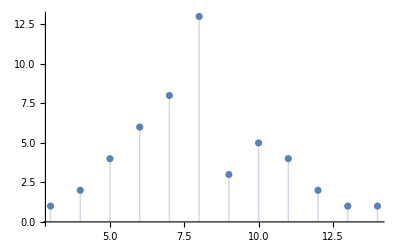

```mathematica
ListPlot[Tally[Map[StringLength,randomWords]],Filling->Axis]
```

It seems we mostly have 8 letter words.

### Question Subsection

Write a function that checks whether a word is a palindrome. Use it on the random word list above to check if any of the words are palindromes. Don’t use the built-in function PalindromeQ.

#### Solution

```mathematica
myPalindromeQ[s_]:=Module[{rs=StringReverse[s]},
SameQ[s,rs]
]
```

```mathematica
myPalindromeQ/@randomWords
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

## Intermediate Exercises

### Question Subsection

In the random word list above, pick out the words that contain the letter a.

#### solution

```mathematica
Select[randomWords,StringContainsQ[#,"a"]&]
```

{awn,lariat,behead,fixation,adjust,entrails,stable,undertaking,pantry,hardcover,fancy,curricular,premeditate,repairer,repeated,bloodstained,tardily,changeless,radially,spiritualistic,scamper,teasing,stargazer,brokenhearted,statutorily,sandwich,champagne,unsteady,grab,barbershop,cause,dairying}

### Question Subsection

Given a real number, use string manipulation to figure out the number of digits before and after the decimal place.

#### Solution

```mathematica
NumReport[r_]:=Module[{s=ToString[r],parts,pre,post},
parts=StringSplit[s,"."];
pre=StringLength@parts[[1]];post=StringLength@parts[[-1]];
Grid[{{"Before Decimal Point","After Decimal Point"},{pre,post}},Frame->All]
]
```

```mathematica
NumReport[32.5452]
```

Before Decimal Point | After Decimal Point
2 | 4

## Advanced Exercises

### Question Subsection

Take the middle four letters of each word from the random word list above, combine them together, and do a distribution plot for all letters. Consider all the pitfalls e.g. some words might be fewer than four characters long.

#### Hint

You will need to finagle with ListPlot options a little bit in order to show the letters on the x-axis. Checkout the two options Frame and FrameTicks to ListPlot.

#### Solution

```mathematica
StringProcess[s_]:=Module[{len=StringLength[s]},
n=Floor[len/2]-1;
If[len<4,"",
StringTake[s,{n,n+3}]
]
]
```

```mathematica
StringSplit["sdf",""]
```

{s,d,f}

```mathematica
letterMapping=MapIndexed[#1->#2[[1]]&,Alphabet[]]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

```mathematica
letterDist=SortBy[Tally[Flatten[Map[StringSplit[StringProcess[#],""]&,randomWords]]],First]
```

{{a,24},{b,4},{c,8},{d,9},{e,23},{f,1},{g,8},{h,4},{i,22},{j,1},{k,1},{l,7},{m,3},{n,12},{o,5},{p,5},{r,20},{s,8},{t,15},{u,10},{v,2},{w,2},{x,1},{y,1}}

```mathematica
ticks = MapIndexed[{#2[[1]],#1}&,Alphabet[]]
```

{{1,a},{2,b},{3,c},{4,d},{5,e},{6,f},{7,g},{8,h},{9,i},{10,j},{11,k},{12,l},{13,m},{14,n},{15,o},{16,p},{17,q},{18,r},{19,s},{20,t},{21,u},{22,v},{23,w},{24,x},{25,y},{26,z}}

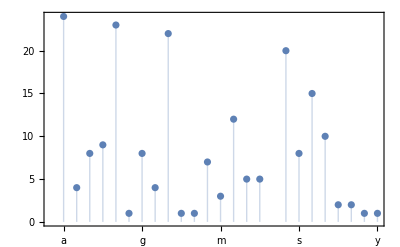

```mathematica
ListPlot[letterDist/.letterMapping,
Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{ticks,None}},
Filling->Axis]
```

### Question Subsection

The following is the story of how John and Jordan met. Make a template out of it so that this could be the story of any two people, and not just John and Jordan.

```mathematica
JJStory="It was a fine sunny day. John was out and about galloping through the grass. John had just finished his work and he was out to enjoy life a little. He came across a bunch of kids who were shooting a soccer ball around. John wanted to play, but he was too shy to ask and join in. With a big sigh, John walked off towards the little creek and sat at the bank. 
He was throwing little rocks in the water and looking at how the ripples crashed into each other when he saw her. She was reading a book. John decided to play a game and guess her name. Was it Maria? No, she didn't look like a Maria. Moira... nahhh. Maryam? Masha? Mary? Mina? Mona? He noticed a theme in his guessing game. John started wondering about why that is. Why was he only thinking of names that started with the letter M? He was deep in thought and didn't realize he was staring at her.
 All of a sudden she said, \"It's Jordan\", and went back to reading. 
\"WHAT???!!!!!!\" Had John been talking out loud? How embarrassing. John didn't know what to do. He was really embarrassed, so he jumped in the water. Yea, John was an awkward dude.";
```

#### Solution

```mathematica
template=StringTemplate[StringReplace[JJStory,{"John"->"`1`","Jordan"->"`2`"}]];
```

```mathematica
template["Jamie","Judy"]
```

It was a fine sunny day. Jamie was out and about galloping through the grass. Jamie had just finished his work and he was out to enjoy life a little. He came across a bunch of kids who were shooting a soccer ball around. Jamie wanted to play, but he was too shy to ask and join in. With a big sigh, Jamie walked off towards the little creek and sat at the bank. 
He was throwing little rocks in the water and looking at how the ripples crashed into each other when he saw her. She was reading a book. Jamie decided to play a game and guess her name. Was it Maria? No, she didn't look like a Maria. Moira... nahhh. Maryam? Masha? Mary? Mina? Mona? He noticed a theme in his guessing game. Jamie started wondering about why that is. Why was he only thinking of names that started with the letter M? He was deep in thought and didn't realize he was staring at her.
 All of a sudden she said, "It's Judy", and went back to reading. 
"WHAT???!!!!!!" Had Jamie been talking out loud? How embarrassing. Jamie didn't know what to do. He was really embarrassed, so he jumped in the water. Yea, Jamie was an awkward dude.